# 2022-07-20

Performing the Sudakov integrals for different splitting functions

## Perform θ-integration

```mathematica
Integrate[1/θ,{θ,pt0/(z*pt1),1},Assumptions->{pt0∈ Reals,pt1∈ Reals , pt1>pt0, pt0>0,z<1, z>0, pt0!=pt1*0.5,pt0<pt1 z}]
```

Log[(pt1 z)/pt0]

## Perform z-integration

## P[z] = 1/z

```mathematica
PgtoggGavin[z_]:=1/z;
```

```mathematica
Integrate[PgtoggGavin[z]Log[(pt1 z)/pt0],{z, pt0/pt1,1},Assumptions->{pt0∈ Reals,pt1∈ Reals , pt1>pt0, pt0>0,z<1, z>0, pt0!=pt1*0.5,pt0<pt1 z}]
```

1/2 Log[pt0/pt1]^2

```mathematica
SudakovGavin[pt1_,pt0_]:=1/2 Log[pt0/pt1]^2
```

```mathematica
ExpSudakovGavin[pt1_,pt0_,CA_,αs_]:=Exp[-(2αs*CA)/π SudakovGavin[pt1,pt0]]
```

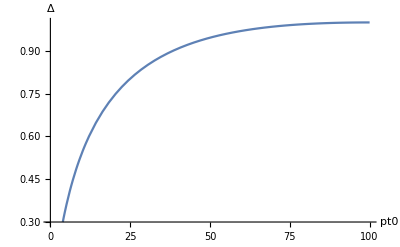

```mathematica
Plot[ExpSudakovGavin[100,pt0,3,0.12],{pt0,0.001,100},AxesLabel->{"pt0","Δ"}]
```

## P[z] = (1-z)/z+(z-z^2)/2

```mathematica
Pgtoggnonsym[z_]:=((1-z)/z+(z-z^2)/2);
```

```mathematica
Integrate[Pgtoggnonsym[z]Log[(pt1 z)/pt0],{z, pt0/pt1,1},Assumptions->{pt0∈ Reals,pt1∈ Reals , pt1>pt0, pt0>0,z<1, z>0, pt0!=pt1*0.5,pt0<pt1 z}]
```

1/72 (-((pt0-pt1) (4 pt0^2-5 pt0 pt1+67 pt1^2))/pt1^3+6 Log[pt0/pt1] (11+6 Log[pt0/pt1]))

```mathematica
Sudakovnonsym[pt1_,pt0_]:=1/72 (-((pt0-pt1) (4 pt0^2-5 pt0 pt1+67 pt1^2))/pt1^3+6 Log[pt0/pt1] (11+6 Log[pt0/pt1]))
```

```mathematica
ExpSudakovnonsym[pt1_,pt0_,CA_,αs_]:=Exp[-(2αs*CA)/π Sudakovnonsym[pt1,pt0]]
```

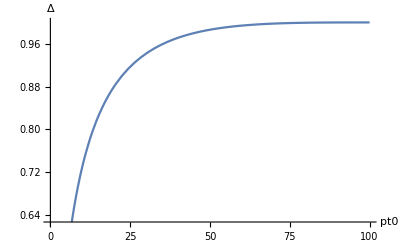

```mathematica
Plot[ExpSudakovnonsym[100,pt0,3,0.12],{pt0,0.001,100},AxesLabel->{"pt0","Δ"}]
```

## P[z] = (1-z)/z+z/(1-z)+z-z^2

```mathematica
PgtoggsymUrs[z_]:=((1-z)/z+z/(1-z)+z-z^2);
```

```mathematica
Integrate[PgtoggsymUrs[z]Log[(pt1 z)/pt0],{z, pt0/pt1,1/2},Assumptions->{pt0∈ Reals,pt1∈ Reals , pt1>pt0, pt0>0,z<1, z>0, pt0!=pt1*0.5,pt0<pt1 z,2 pt0<pt1}]
```

137/144-π^2/4-pt0^3/(9 pt1^3)+pt0^2/(4 pt1^2)-(2 pt0)/pt1+(11 Log[2])/12-2 Log[2]^2+1/4 Log[2] Log[256]+((pt0 (2 pt0^2-3 pt0 pt1+12 pt1^2))/(6 pt1^3)+Log[1-pt0/pt1]) Log[pt0/pt1]-1/2 Log[pt0/pt1]^2-Log[pt1]^2-11/12 Log[pt1/pt0]+(pt0^3 Log[pt1/pt0])/(3 pt1^3)-(pt0^2 Log[pt1/pt0])/(2 pt1^2)+(2 pt0 Log[pt1/pt0])/pt1+Log[2] Log[pt1/pt0]+1/3 Log[8] Log[pt1/pt0]-2 Log[2-(2 pt0)/pt1] Log[pt1/pt0]+2 Log[1-pt0/pt1] Log[pt1/pt0]-Log[-pt0/(pt0-pt1)] Log[pt1/pt0]+ⅈ π Log[pt1/(-pt0+pt1)]+Log[pt0] Log[pt1/(-pt0+pt1)]+1/2 Log[pt1/(-pt0+pt1)]^2+Log[pt1] Log[-pt0+pt1]+PolyLog[2,-pt1/(pt0-pt1)]

```mathematica
SudakovsymUrs[pt1_,pt0_]:=137/144-π^2/4-pt0^3/(9 pt1^3)+pt0^2/(4 pt1^2)-(2 pt0)/pt1+(11 Log[2])/12-2 Log[2]^2+1/4 Log[2] Log[256]+((pt0 (2 pt0^2-3 pt0 pt1+12 pt1^2))/(6 pt1^3)+Log[1-pt0/pt1]) Log[pt0/pt1]-1/2 Log[pt0/pt1]^2-Log[pt1]^2-11/12 Log[pt1/pt0]+(pt0^3 Log[pt1/pt0])/(3 pt1^3)-(pt0^2 Log[pt1/pt0])/(2 pt1^2)+(2 pt0 Log[pt1/pt0])/pt1+Log[2] Log[pt1/pt0]+1/3 Log[8] Log[pt1/pt0]-2 Log[2-(2 pt0)/pt1] Log[pt1/pt0]+2 Log[1-pt0/pt1] Log[pt1/pt0]-Log[-pt0/(pt0-pt1)] Log[pt1/pt0]+ⅈ π Log[pt1/(-pt0+pt1)]+Log[pt0] Log[pt1/(-pt0+pt1)]+1/2 Log[pt1/(-pt0+pt1)]^2+Log[pt1] Log[-pt0+pt1]+PolyLog[2,-pt1/(pt0-pt1)]
```

```mathematica
ExpSudakovsymUrs[pt1_,pt0_,CA_,αs_]:=Exp[-(4*αs*CA)/π SudakovsymUrs[pt1,pt0]]
```

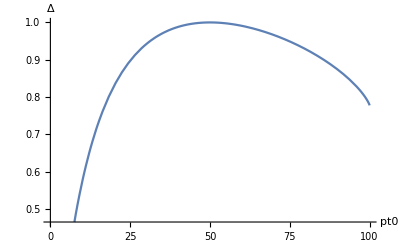

```mathematica
Plot[ExpSudakovsymUrs[100,pt0,3,0.12],{pt0,0.001,100},AxesLabel->{"pt0","Δ"}]
```

## Plot together

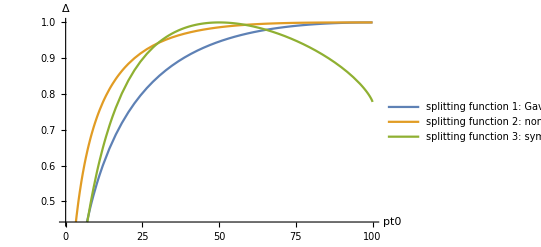

```mathematica
Plot[{ExpSudakovGavin[100,pt0,3,0.12],ExpSudakovnonsym[100,pt0,3,0.12],ExpSudakovsymUrs[100,pt0,3,0.12]},{pt0,0.001,100},AxesLabel->{"pt0","Δ"},PlotLegends->{"splitting function 1: Gavin (Eq. 25)","splitting function 2: non-sym (Eq. 27)","splitting function 3: sym (Eq. 29)"}]
```